## Import the data

If the data stored in “goodmuon2.txt” is contained in the same directory as the mathematica notebook then this filename will work

```mathematica
filename = StringJoin[NotebookDirectory[],"goodmuon2.txt"]
```

C:\SugarSync\Ben\CU Optics Lab\2011 Course Artifacts\Mathematica\goodmuon2.txt

```mathematica
goodmuon2 = Import[filename, "Table"];
```

Show the first 10 rows in “TableForm”

```mathematica
goodmuon2[[1;;10,;;]]//TableForm
```

0: | 4. | 1. | 87. | 54.
4: | 32. | 6352. | 1751. | 1541.
8: | 1309. | 1216. | 1168. | 989.
12: | 935. | 864. | 799. | 748.
16: | 747. | 700. | 625. | 605.
20: | 579. | 574. | 580. | 549.
24: | 516. | 477. | 473. | 417.
28: | 465. | 376. | 394. | 393.
32: | 374. | 348. | 316. | 314.
36: | 323. | 297. | 288. | 274.

Select out all rows, taking only columns 2 through 5.
Flatten the table into one long list.

```mathematica
goodmuon3 = Flatten[goodmuon2[[;;,2;;5]]];
goodmuon3[[1;;8]]//TableForm
```

4.
1.
87.
54.
32.
6352.
1751.
1541.

## Construct time array, data table, and weights

According to Jason and Brian the time step was 0.095 microseconds.  
Construct the time array.

```mathematica
dt = 0.095*^-6  ; (*time steps in seconds*)
time = Table[dt*i,{i,1,Length[goodmuon3]}];
```

ListPlot[] requires pairs of (x,y) values for plotting, so this table constructs an array of the appropriate form:

{{9.5×10^-8,4.},{1.9×10^-7,1.},{2.85×10^-7,87.},{3.8×10^-7,54.},{4.75×10^-7,32.},{5.7×10^-7,6352.}}

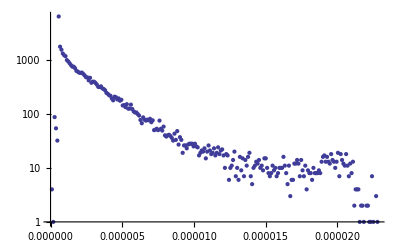

```mathematica
data = Transpose[{time,goodmuon3}];
data[[1;;6]](*Display the first few points*)
ListLogPlot[data,PlotRange->All]
```

The first few data points look questinoable.  Call the trimmed data set “datatrimmed”

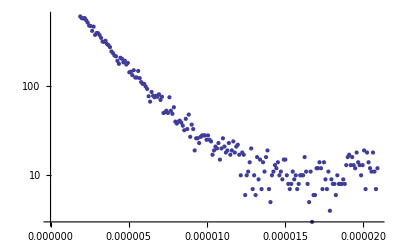

```mathematica
dataTrimmed = data[[20;;220]];
ListLogPlot[dataTrimmed,PlotRange->All]
```

Construct the weights array using the following form for a Possion distribution

weights=1/σ^2=1/(number of counts)
error = σ = √(number of counts)

The “number of counts” is given in the second column of the array “datatrimmed”.

```mathematica
error = √dataTrimmed[[;;,2]]; 
weights = 1/error^2  ;
```

## Make a plot with error bars

### I am ashamed to say it, but Mathematica can only make error bars on plots with linear-linear axes

### Installing the Mathematica “Error Bar Log Plots Package”

The download is from http://library.wolfram.com/infocenter/MathSource/6747/
Title		Error Bar Log Plots for Mathematica 6
Author	Frank Rice
Organization: 	California Institute of Technology
Department: 	Physics
Revision date:	2007-05-29
Description:		
ErrorBarLogPlots.m is a package which adds log-scale plotting functions similar to the standard ErrorListPlot provided in Mathematica 6. The added functions are ErrorListLogPlot, ErrorListLogLinearPlot, and ErrorListLogLogPlot.

To install the package you have two options:
1) Open the notebook “ErrorBarLogPlots_Installer.nb” which is part of the download and let it auto-run to install the package.
2) 	(a) Go to File->Install..   
	(b) Select Type of Item to Install “Package”
	(c) Select Source “From File”
	(d) Navigate to where the package was downloaded and select the package “ErrorBarLogPlots.m”
	(e) Select “OK”

### Loading and Using the ErrorBarLogPlots package

This loads the package so the new functions can be called

```mathematica
Needs["ErrorBarLogPlots`"]
```

Here is the help entry for ErrorListLogPlot

```mathematica
?ErrorListLogPlot
```

RowBox[{"ErrorListLogPlot", "[", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["dy", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]], ",", SubscriptBox[StyleBox["dy", "TI"], StyleBox["2", "TR"]]}], "}"}], ",", StyleBox["…", "TI"]}], "}"}], "]"}] makes a log plot of points corresponding to a list of values RowBox[{SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]], ",", " ", SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]], ",", " ", StyleBox["…", "TR"]}], with corresponding error bars. The errors have magnitudes RowBox[{SubscriptBox[StyleBox["dy", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["dy", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}].
RowBox[{"ErrorListLogPlot", "[", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", RowBox[{"ErrorBar", "[", SubscriptBox[StyleBox["err", "TI"], "1"], "]"}]}], "}"}], ",", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]]}], "}"}], ",", RowBox[{"ErrorBar", "[", SubscriptBox[StyleBox["err", "TI"], StyleBox["2", "TR"]], "]"}]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] makes a log plot of points with specified StyleBox["x", "TI"] and StyleBox["y", "TI"] coordinates and error magnitudes.

Before the plot can be made, and appropriate array of data and ErrorBars must be constructed:
the form is { {{x1,y1},ErrorBar[e1]}, {{x2,y2},ErrorBar[e2]},... }

```mathematica
dataTrimmedError = Table[{dataTrimmed[[i]],ErrorBar[ error[[i]] ]},{i,1,Length[dataTrimmed]}];
dataTrimmedError[[1;;5]]
```

{{{1.9×10^-6,605.},ErrorBar[24.5967]},{{1.995×10^-6,579.},ErrorBar[24.0624]},{{2.09×10^-6,574.},ErrorBar[23.9583]},{{2.185×10^-6,580.},ErrorBar[24.0832]},{{2.28×10^-6,549.},ErrorBar[23.4307]}}

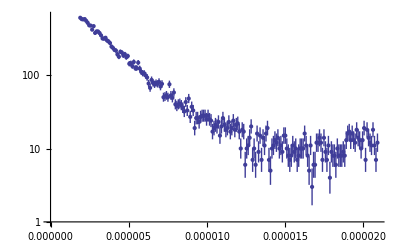

```mathematica
dataErrorPlot = ErrorListLogPlot[dataTrimmedError]
```

## Fitting

LinearModelFit  and NonlinearModelFit are the two best fitting function in Mathematica.  They return a function which can be evaluated and also a set of properties which are documented in the help for getting the parameter errors and covariance matrix.

FittedModel[8.61781+1501.19 ⅇ^(-464334. t)]

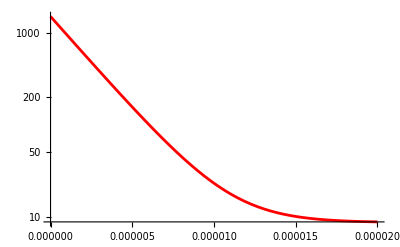

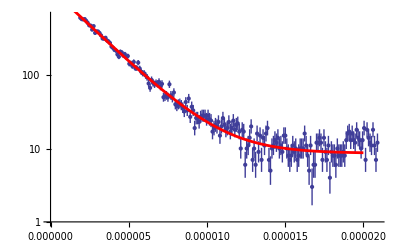

```mathematica
fit =NonlinearModelFit[dataTrimmed,A*Exp[-t/τ]+C,{{A,5000},{τ,2*^-6},{C,5}},t,Weights->weights]
fitplot = LogPlot[fit[t],{t,0,20*^-6},PlotRange->All,PlotStyle->{Thickness[0.005], Red}]
Show[dataErrorPlot,fitplot]
```

### Nice and common ways to display the fit parameters and errors

A more complete list of the properties is found in the help or at http://reference.wolfram.com/mathematica/ref/NonlinearModelFit.html  
Look under the “MORE INFORMATION” section.

```mathematica
fit["BestFitParameters"]
fit["ParameterErrors"]
fit["ParameterTable"]
fit["CovarianceMatrix"]//TableForm
```

{A→1501.19,τ→2.15362×10^-6,C→8.61781}

{35.3188,2.76523×10^-8,0.377443}

| Estimate | Standard Error | t-Statistic | P-Value
A | 1501.19 | 35.3188 | 42.5039 | 1.75765×10^-101
τ | 2.15362×10^-6 | 2.76523×10^-8 | 77.8821 | 1.7543×10^-150
C | 8.61781 | 0.377443 | 22.8321 | 2.27899×10^-57

1247.42 | -8.86652×10^-7 | 4.57414
-8.86652×10^-7 | 7.64652×10^-16 | -4.97338×10^-9
4.57414 | -4.97338×10^-9 | 0.142463

## Modestly Sweeter Looking Plots in Mathematica

You can comment or uncomment any of the lines in plotOptions below to see what effect it has on the aesthetic appeal of the graph.
This is a very convenient way to handle plot options in Mathematica, because this plotOptions list which I created can be reused for many plots without retyping a bunch of options.

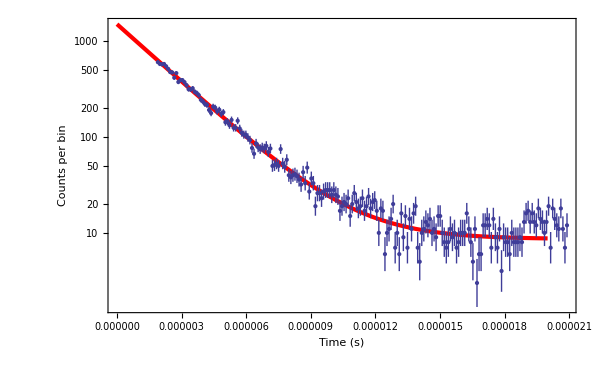

```mathematica
plotOptions = {Frame->True,
PlotRange->All,
FrameLabel->{"Time (s)", "Counts per bin"},
(*GridLines->Automatic,*)
Axes->None,
LabelStyle->{FontFamily->"Arial", FontSize->12},
ImageSize->600};
Show[fitplot,dataErrorPlot,plotOptions]
```

The annotated plot shown below took a few additional quick steps:
1) Copy the plot above and paste it into a new cell (This is optional, but prevents the annotated plot from being rewritten if the Show statement is re-executed)
2) Copy the Table of fit parameters from above, and paste it into the plot
3) Open up the Drawing Tools by right clicking on the plot and selecting “Drawing Tools”.-Graphics-
4) Click on the “Mathematical Text” button that looks like -Graphics-